# Nested Sampling analyis of celtic burial data

```mathematica
<<BayesianInference`
```

```mathematica
defineInferenceProblem[]
```

{Data,Parameters,IndependentVariables,LogLikelihoodFunction,LogPriorPDFFunction,GeneratingDistribution,PriorDistribution,LogPriorPDF}

### Full and Half Sibling model

Parameters:

ageH

ageA

birthAgeH

birthAgeA

mothersBirthDate

```mathematica
logLSiblings[paramVector_]:=Module[{ageH,ageA,birthAgeH,birthAgeA,mothersBirthDate,burialDateH,burialDateA,burialDateHdist,burialDateAdist},
{ageH,ageA,birthAgeH,birthAgeA,mothersBirthDate}=paramVector;
burialDateHdist=NormalDistribution[-530.,6];
burialDateAdist=NormalDistribution[-490.,6];
burialDateH=mothersBirthDate+birthAgeH+ageH;
burialDateA=mothersBirthDate+birthAgeA+ageA;
LogLikelihood[burialDateHdist,{burialDateH}]+LogLikelihood[burialDateAdist,{burialDateA}]
]
```

```mathematica
logPriorSiblings[paramVector_]:=Module[{ageH,ageA,birthAgeH,birthAgeA,mothersBirthDate},
{ageH,ageA,birthAgeH,birthAgeA,mothersBirthDate}=paramVector;
LogLikelihood[NormalDistribution[45.,6],{ageH}]+
LogLikelihood[NormalDistribution[30.,6],{ageA}]+
LogLikelihood[NormalDistribution[30.,6],{birthAgeH,birthAgeA}]+
LogLikelihood[UniformDistribution[{-600,-400}],{mothersBirthDate}]
]
```

```mathematica
logLSiblings[{20,20,20,20,-550}]
```

-16.5325

```mathematica
logPriorSiblings[{20,20,20,20,-550}]
```

-28.9883

```mathematica
infObjSiblings=inferenceObject[<|
"Parameters"->{{ageH,0,100},{ageA,0,100},{birthAgeH,0,100},{birthAgeA,0,100},{mothersBirthDate,-600,-400}},
"LogLikelihoodFunction"->logLSiblings,
"LogPriorPDFFunction"->logPriorSiblings,
"StartingPoints"->{20,30,15,45,-565}|>
]
```

inferenceObject[…]

```mathematica
resultSiblings=nestedSampling[infObjSiblings]
```

Generated 100 inital samples using MCMC. Acceptance rate: 0.20112

RandomVariate::precw: The precision of the argument function (2.7833335197159×10^309) is less than WorkingPrecision (MachinePrecision).

RandomVariate::precw: The precision of the argument function (-7.8992900375274×10^310) is less than WorkingPrecision (MachinePrecision).

RandomVariate::precw: The precision of the argument function (2.2342305091511×10^312) is less than WorkingPrecision (MachinePrecision).

General::stop: Further output of RandomVariate::precw will be suppressed during this calculation.

Divide::infy: Infinite expression (1.48447042858543×10^545)/(0``-674.8194264176194) encountered.

Divide::infy: Infinite expression -(5.×10^674)/(0``-674.8194264176194) encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Less::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of Less::nord will be suppressed during this calculation.

LinearAlgebra`Private`CholeskyUpdateInplace::mindet: Input matrix contains an indeterminate entry.

General::stop: Further output of LinearAlgebra`Private`CholeskyUpdateInplace::mindet will be suppressed during this calculation.

Divide::infy: Infinite expression (9.84964383235629×10^846)/(0``-866.7938970130399) encountered.

General::stop: Further output of Divide::infy will be suppressed during this calculation.

inferenceObject[<|Parameters -> {{ageH, 0, 100}, {ageA, 0, 100}, {birthAgeH, 0, 100}, {birthAgeA, 0, 100}, {mothersBirthDate, -600, -400}}, LogLikelihoodFunction -> logLSiblings, LogPriorPDFFunction -> logPriorSiblings, <<12>>, RelativeEntropy -> <|Mean -> 5.08909, StandardError -> 0.206677|>, EmpiricalPosteriorDistribution -> DataDistribution[<<Empirical>>, {783, 5}]|>]

```mathematica
resultSiblings["Properties"]
```

{CrudeLogEvidence,CrudeRelativeEntropy,EmpiricalPosteriorDistribution,GeneratedNestedSamples,LogEstimatedMissingEvidence,LogEvidence,LogLikelihoodFunction,LogLikelihoodMaximum,LogPriorPDFFunction,ParameterExpectedValues,ParameterRanges,Parameters,Properties,RelativeEntropy,SamplePoolSize,Samples,StartingPoints,TotalSamples}

```mathematica
resultSiblings["LogEvidence"]
```

<|Mean→-14.5874,StandardError→0.209456|>

```mathematica
resultSiblings["ParameterExpectedValues"]
```

<|ageH→<|Mean→38.2409,StandardError→0.215496|>,ageA→<|Mean→37.9218,StandardError→0.22387|>,birthAgeH→<|Mean→22.5634,StandardError→0.326039|>,birthAgeA→<|Mean→40.8902,StandardError→0.28635|>,mothersBirthDate→<|Mean→-579.868,StandardError→0.536812|>|>

```mathematica
resultSiblings["EmpiricalPosteriorDistribution"]
```

DataDistribution[…]

```mathematica
post=resultSiblings["EmpiricalPosteriorDistribution"]
```

DataDistribution[…]

```mathematica
Mean[post]
```

{38.2303,37.8771,22.5695,40.9305,-579.867}

```mathematica
Covariance[post]
```

{{14.4679,12.2245,8.20495,5.37108,-27.1889},{12.2245,23.5799,13.0879,3.89064,-30.2349},{8.20495,13.0879,33.1066,25.6326,-39.7887},{5.37108,3.89064,25.6326,30.5188,-30.2135},{-27.1889,-30.2349,-39.7887,-30.2135,90.2827}}

```mathematica
samples=RandomVariate[post,1000];
```

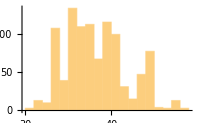
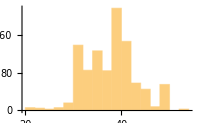
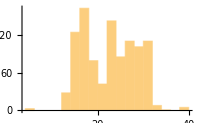
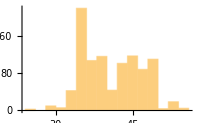
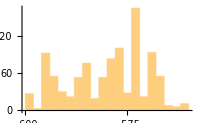

```mathematica
Row@Table[Histogram[samples[[All,i]],ImageSize->200],{i,1,5}]
```

```mathematica
Table[Quantile[samples[[All,i]],#]&/@{0.05,0.95},{i,5}]
```

{{-28.9304,90.6136},{-6.6217,66.4347},{-29.5303,78.9537},{-15.9411,97.9508},{-597.573,-492.742}}